# Avance

## Inicialización

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

### Información de los paquetes cargados

```mathematica
?AdvancedMapping`*
```

```mathematica
?EconomicComputations`*
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

```mathematica
Length[database]
```

4

```mathematica
First[database]//Keys(*Nos devuelve todo lo que incluye la base de datos en forma de asociación de lista*)
```

{Name,Dates,Prices,DatedPrices,Returns,TrendReturns,VelocityTrendReturns,DatedReturns,DatedTrendReturns,DatedVelocityTrendReturns}

```mathematica
First[database]["Prices"] // First(*aqui estamos accediendo al primer elemento de la base de datos, es decir, DWJ*)
```

1606.2

```mathematica
First[database]["Dates"] // Last
```

```mathematica
database[[1]]["Name"] (*asi podemos accesar a cualquier mercado*)
```

DJIA

```mathematica
Returns[First[database]["Prices"]]
```

```mathematica
First[database]//Keys
```

{Name,Dates,Prices,DatedPrices,Returns,TrendReturns,VelocityTrendReturns,DatedReturns,DatedTrendReturns,DatedVelocityTrendReturns}

```mathematica
dowJones=First[database];
Keys[dowJones]
```

```mathematica
database[[1]]["Name"]
```

DJIA

{Name,Dates,Prices,DatedPrices,Returns,TrendReturns,VelocityTrendReturns,DatedReturns,DatedTrendReturns,DatedVelocityTrendReturns}

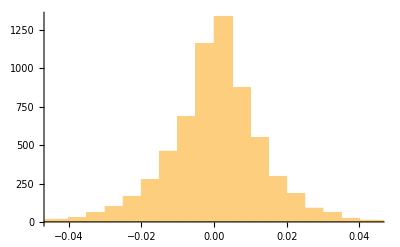

```mathematica
{"Name","Dates","Prices","DatedPrices","Returns","TrendReturns","VelocityTrendReturns","DatedReturns","DatedTrendReturns","DatedVelocityTrendReturns"}
dowJones["Returns"]//Histogram(*Al aplicar retornos se ve una distribucion masomenos normal, ya que gracias a los retornos se resuelve el problema de la no estacionaridad de los precios *)
```

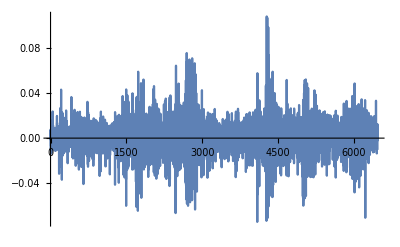

```mathematica
ListLinePlot[dowJones["Returns"],PlotRange->All]
```

```mathematica
(*Pero estos son numeros continuos, y necesitamos discretizar, o sea que se convierta en un entero*)
```

{-0.00650255,0.000879896,0.00763187}

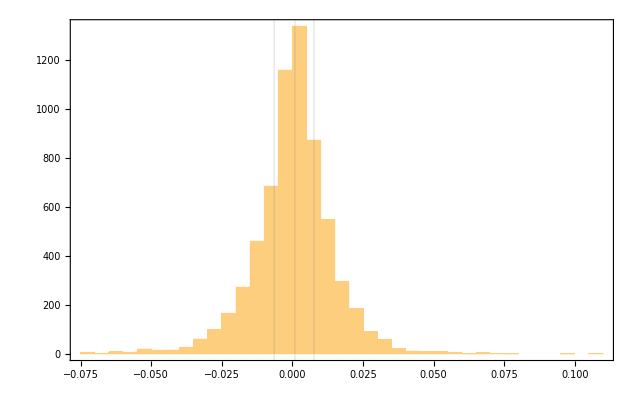

```mathematica
cuartiles=Quantile[dowJones["Returns"],{1/4,1/2,3/4}]
Histogram[dowJones["Returns"],GridLines->{cuartiles,{}},PlotRange-> All,Frame-> True]
```

```mathematica
(*por cada particion que agarramos tenenmos la misma cantidad de probabilidad, se muestra el histograma puntos/lineas equiprobables*)
```

```mathematica
(*Join une listas, la lista llamada cuartiles da el valor del punto de la primera linea vertical, el valor del punto de la segunda linea vertical, y el valor de la tercera linea vertical*)
```

```mathematica
(*para agrupar, se tienen que considerar los valores extremos que aparecen en el histograma *)
intervalos=Partition[Join[{-∞},cuartiles,{∞}],2,1](*Particion de dos en dos pero con un paso de 1 en 1*)
```

{{-∞,-0.00650255},{-0.00650255,0.000879896},{0.000879896,0.00763187},{0.00763187,∞}}

```mathematica
(*A continuación etiquetamos cada separación de intervalo para terminar de discretizar*)
```

```mathematica
discreteStates=Range[Length[intervalos]](*Aqui se muestra la lista con los ya separados intervalos discretizados*)
```

{1,2,3,4}

```mathematica
intervalos[[1]]
```

{-∞,-0.00650255}

```mathematica
Interval[intervalos[[1]]]
```

Interval[{-∞,-0.00650255}]

```mathematica
(*A continuacion se van a sustituir-remplazar-sustituir los elementos de la lista, son las reglas para obtener los valores discretizados*)
```

```mathematica
(*con x_ se prueban valores de los retornos de los precios, con IntervalMemberQ se verifica si el valor x pertenece o no al primer intervalo, si pertenece lo etiqueta como 1*)
regla1=(x_/;IntervalMemberQ[Interval[intervalos[[1]]],x])->discreteStates[[1]];(*Aqui se asigna al primer intervalo el valor discreto 1*)
```

```mathematica
regla2=(x_/;IntervalMemberQ[Interval[intervalos[[2]]],x])->discreteStates[[2]];(*Aqui se asigna al segundo intervalo el valor discreto 2*)
```

```mathematica
regla3=(x_/;IntervalMemberQ[Interval[intervalos[[3]]],x])->discreteStates[[3]];(*Aqui se asigna al tercer intervalo el valor discreto 3*)
```

```mathematica
regla4=(x_/;IntervalMemberQ[Interval[intervalos[[4]]],x])->discreteStates[[4]];(*Aqui se asigna al cuarto intervalo el valor discreto 4*)
```

```mathematica
Take[dowJones["Returns"],20]/.{regla1,regla2,regla3,regla4}(*Aqui se muestran los valores discretos para estos retornos hechos a partir de la serie de tiempo*)
```

{3,3,3,2,3,1,1,2,3,1,4,1,3,1,1,3,4,2,3,2}

```mathematica
dowJones["Returns"]/.{regla1,regla2,regla3,regla4};
```

```mathematica
reglas=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalos,discreteStates}](*Permite mapear dos listas x -> y *)
dowJonesDiscreto=dowJones["Returns"]/.reglas;(*Con esto ya tenemos discretizado los retornos de la serie de tiempo DWJ *)
```

{x_/;IntervalMemberQ[Interval[{-∞,-0.00650255}],x]→1,x_/;IntervalMemberQ[Interval[{-0.00650255,0.000879896}],x]→2,x_/;IntervalMemberQ[Interval[{0.000879896,0.00763187}],x]→3,x_/;IntervalMemberQ[Interval[{0.00763187,∞}],x]→4}

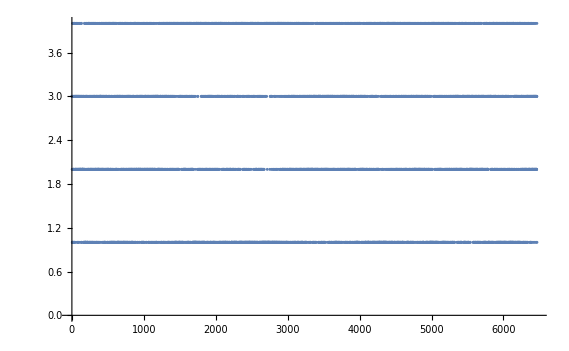

```mathematica
ListPlot[dowJonesDiscreto]
```

```mathematica
N[Entropy[dowJonesDiscreto]](*Esta es la entropia de toda la serie de tiempo*)
```

1.38629

```mathematica
(*Ahora hay que obtener las fechas en que sucedió cada retorno*)
```

```mathematica
discretoConFechas=Transpose[{Drop[dowJones["Dates"],-1],dowJonesDiscreto}](*Transpose se hace para tener fecha y valor discreto del retorno, -1 pq los retornos siempre eliminan un dato*)
```

{{Day: Fri 8 Nov 1991,3},{Day: Mon 11 Nov 1991,3},{Day: Tue 12 Nov 1991,3},{Day: Wed 13 Nov 1991,2},{Day: Thu 14 Nov 1991,3},6455,{Day: Mon 29 May 2017,2},{Day: Tue 30 May 2017,3},{Day: Wed 31 May 2017,3},{Day: Thu 1 Jun 2017,4},{Day: Fri 2 Jun 2017,1}}
 |  |  |  |

```mathematica
parts=Partition[discretoConFechas,50,1];(*Nuestra ventana de tiempo es de 50, el mnumero uno significa que va cambiando de un dia en un día, es decir, que el paso es de uno en uno, pero que agrupa 50 días en 50 días*)
```

```mathematica
Length[parts]
Last[parts[[1]][[All,1]]](*ultimo elemento de la particion 1 y columna 1, sirve para obtener la ultima fecha*)
```

6416

Day: Fri 24 Jan 1992

```mathematica
Manipulate[DateListPlot[parts[[i]],Joined->False],{i,1,Length[parts],1}](*Cada ventana tiene 50 muestras, cada particion muestra su valor discretizado*)
```

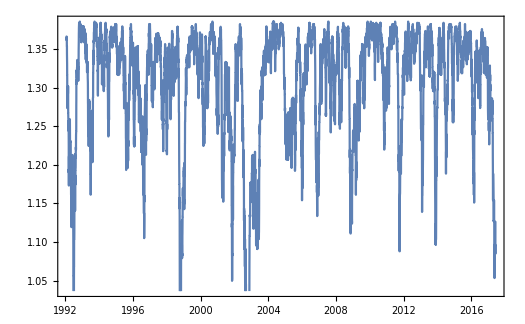

6416

```mathematica
(*Ahora vamos a imprimir los pares de fechas y entropias en esas ventanan de tiempo de 50 dias*)
resultado=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,parts];(*All,1 nos da la ultima fecha de la columna de fechas, All,2 nos da los valores discretizados de los retornos en esa ventana de tiempo de 50*)
DateListPlot[resultado]
Length[resultado]
(*Esta grafica muestra la entropia historica de DWJ, la entropia es el resultado del retorno discretizado de la serie de tiempo*)
```

```mathematica
Discretizar[retornos_]:=Block[{cuartiles,intervalos,discreteStates,reglas,resultado},
cuartiles=Quantile[retornos,{1/4,1/2,3/4}];
intervalos=Partition[Join[{-∞},cuartiles,{∞}],2,1];
discreteStates=Range[Length[intervalos]];
reglas=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalos,discreteStates}];

resultado=retornos/.reglas;
Return[resultado];
];

EntropiaRetornosDiscretos[mercado_,window_:30]:=
Block[{dowJonesDiscreto,discretoConFechas,parts,resultado},
dowJonesDiscreto=Discretizar[mercado["Returns"]];
discretoConFechas=Transpose[{Drop[mercado["Dates"],-1],dowJonesDiscreto}];
parts=Partition[discretoConFechas,window,1];
resultado=Map[
{
Last[#[[All,1]]],
N[Entropy[#[[All,2]]]]
}&,
parts
];
Return[resultado];
];
```

```mathematica
market = database[[2]];
```

```mathematica
EntropiaRetornosDiscretos[database[[2]],252]
```

{{Day: Thu 5 Nov 1992,1.37618},{Day: Fri 6 Nov 1992,1.37618},{Day: Mon 9 Nov 1992,1.3769},6190,{Day: Tue 18 Apr 2017,1.2931},{Day: Wed 19 Apr 2017,1.29573},{Day: Thu 20 Apr 2017,1.29141}}
 |  |  |  |

```mathematica
entropiaMercados = Map[EntropiaRetornosDiscretos[#,252]&,database];
```

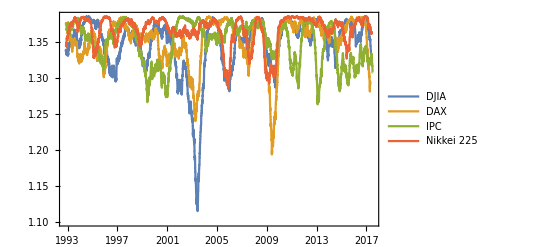

```mathematica
DateListPlot[entropiaMercados,PlotLegends->database[[All,"Name"]],PlotRange->All]
```

```mathematica
entropiaMXX=Map[EntropiaRetornosDiscretos["DAX",252],database];
```

Join::heads: Heads List and Quantile at positions 1 and 2 are expected to be the same.

Join::heads: Heads Quantile and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

MapThread::mptd: Object Join[{-∞},Quantile[DAX[Returns],{1/4,1/2,3/4}],Quantile[DAX[Returns],{1/4,1/2,3/4}],{∞}] at position {2, 1} in MapThread[x_/;IntervalMemberQ[Interval[#1],x]→#2&,{Join[{-∞},Quantile[DAX[Returns],{1/4,1/2,3/4}],Quantile[DAX[Returns],{1/4,1/2,3/4}],{∞}],{1,2,3,4}}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[x_/;IntervalMemberQ[Interval[Slot[«1»]],x]→#2&,{Join[{-∞},Quantile[DAX[Returns],{1/4,1/2,3/4}],Quantile[DAX[Returns],{1/4,1/2,3/4}],{∞}],{1,2,3,4}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Transpose::nmtx: The first two levels of {DAX[],DAX[Returns]/.MapThread[x_/;IntervalMemberQ[Interval[«1»],x]→#2&,{Join[{-∞},Quantile[DAX[Returns],{1/4,1/2,3/4}],Quantile[DAX[Returns],{1/4,1/2,3/4}],{∞}],{1,2,3,4}}]} cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

# Apéndice de cosas que he calculado

## Esto fue sacado de MXX.nb

```mathematica
N[Entropy[ipcDiscreto]]
```

Entropy::targ: Argument ipcDiscreto at position 1 should be a List, a SparseArray, or a String.

Entropy[ipcDiscreto]

```mathematica
p=Partition[ipcDiscreto,30,1];
po=Map[Entropy,p];
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Entropy::targ: Argument ipcDiscreto at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 30 at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1 at position 1 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30],Entropy[1]].

```mathematica
Histogram[{po},PlotLabel->"Histograma de entropía para entropia real",BaseStyle->FontSize->16](*Length[po] arroja 6380 datos*)
```

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

-Graphics-

```mathematica
Length[po]
```

3

```mathematica
Length[entropiaSimulada]
```

0

```mathematica
ListLinePlot[{(po^2-entropiaSimulada^2),po-entropiaSimulada},PlotLegends->{"x^2-y^2","Entropía real - simulada"},PlotRange->{-2,2},BaseStyle->FontSize->16]
```

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

General::stop: Further output of Partition::ilsmn will be suppressed during this calculation.

-Graphics-

```mathematica
Transpose[{Partition[Drop[ipc["Dates"],-1],30,1],po}];
```

Transpose::nmtx: The first two levels of {ipc[],Partition[Entropy[ipcDiscreto],Entropy[30],Entropy[1]]} cannot be transposed.

```mathematica
Length[po^2-entropiaSimulada^2]
```

2

```mathematica
Length[partsEficientes];(*Esto arroja 6380*)
Length[Partition[Drop[ipc["Dates"],-1],30,1]];(*Esto arroja 6380*)
```

Haciendo una simulacion con una caminata aleatoria encuentro que para un intervalo de confianza de 0.95 se encuentra que la entropia es

```mathematica
N[Quantile[RandomVariate[NormalDistribution[],100000],0.05]]
```

-1.65241

```mathematica
x=Take[N[po],3];
y=Take[N[entropiaSimulada],3];
Take[Abs[N[po-entropiaSimulada]]^2,3];
Histogram[√Take[Abs[N[po-Map[Entropy,Partition[DiscretizeByQuartiles[database[[3]]["Returns"]],30,1]]]]^2,All]]
```

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Take::normal: Nonatomic expression expected at position 1 in Take[entropiaSimulada,3].

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Take::take: Cannot take positions 1 through 3 in Abs[-1. entropiaSimulada+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]]^2.

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

General::stop: Further output of Partition::ilsmn will be suppressed during this calculation.

-Graphics-

```mathematica
res[[All,2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
res[[All,2]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Take[res,5]
Transpose[{Drop[ipc["Dates"],-1],√Take[Abs[N[po-Map[Entropy,Partition[DiscretizeByQuartiles[database[[3]]["Returns"]],30,1]]]]^2,All]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[res,5].

Take[res,5]

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

General::stop: Further output of Partition::ilsmn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {ipc[],{Abs[-1.37511+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]],Abs[-1.37511+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]],«47»,Abs[-1.30136+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]],«6330»}} cannot be transposed.

Transpose[{ipc[],{Abs[-1.37511+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]],Abs[-1.37511+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]],6377,Abs[-1.08326+Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]]]}}]
 |  |  |  |

```mathematica
N[Map[Entropy,{discretSimulados}]]
```

Entropy::targ: Argument discretSimulados at position 1 should be a List, a SparseArray, or a String.

{Entropy[discretSimulados]}

```mathematica
ListLinePlot[√Take[Abs[N[po-Map[Entropy,Partition[DiscretizeByQuartiles[database[[3]]["Returns"]],30,1]]]]^2,All],PlotRange->{-0.01,0.7},PlotLabel->"Diferencia entropia real-entropía simulada"]
```

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

Entropy::targ: Argument 1. at position 1 should be a List, a SparseArray, or a String.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

Entropy::targ: Argument 30. at position 1 should be a List, a SparseArray, or a String.

General::stop: Further output of Entropy::targ will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[Entropy[ipcDiscreto],Entropy[30.],Entropy[1.]].

General::stop: Further output of Partition::ilsmn will be suppressed during this calculation.

-Graphics-

```mathematica
ListLinePlot[√Take[Abs[N[ipc["Returns"]-retornoSimulados]]^2,All],PlotRange->All,PlotLabel->"Diferencia retornos reales-retornos simulados"]
```

ListLinePlot::lpn: Abs[-1. retornoSimulados+ipc[Returns]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot::lpn will be suppressed during this calculation.

ListLinePlot[Abs[-1. retornoSimulados+ipc[Returns]],PlotRange→All,PlotLabel→Diferencia retornos reales-retornos simulados]

```mathematica
N[Quantile[Map[N[Entropy[#[[All,2]]]]&,parts],0.05]](*Con el 95% de confianza de que lo que esta debajo de la linea NO ES GAUSSIANO*)
```

1.15142

```mathematica
DateListPlot[res,GridLines->{{},{1.1219416608504376}},PlotRange->All](*Todo lo que esta debajo de esa linea no es gaussiano*)
```

DateListPlot::ldata: res is not a valid dataset or list of datasets.

DateListPlot[res,GridLines→{{},{1.12194}},PlotRange→All]

Select::normal: Nonatomic expression expected at position 1 in Select[res,Last[#1]<1.12194&].

Part::partd: Part specification Select[res,Last[#1]<1.12194&]⟦All,1⟧ is longer than depth of object.

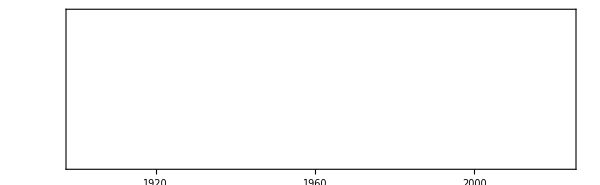

```mathematica
NoGaussians=Select[res,Last[#]<1.1219416608504376 &];
TimelinePlot[NoGaussians[[All,1]]]
```

```mathematica
Length[NoGaussians][[All,2]]
```

Integer[]

```mathematica
Length[res[[All,2]]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

0

```mathematica
(*Dividiendo los datos no gaussianos entre todo los datos del IPC *)
N[Length[NoGaussians[[All,2]]]/Length[res[[All,2]]]]
```

Part::partd: Part specification Select[res,Last[#1]<1.12194&]⟦All,2⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
0.049529780564263326(*Significa que el 4.9% de los datos no se comporta gaussianamente*)
```

0.0495298

```mathematica
ListLinePlot[1.1219416608504376-NoGaussians[[All,2]]]
```

Part::partd: Part specification Select[res,Last[#1]<1.12194&]⟦All,2⟧ is longer than depth of object.

ListLinePlot::lpn: 1.12194-1. Select[res,Last[Slot[«1»]]<1.12194&]⟦All,2⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[1.12194-Select[res,Last[#1]<1.12194&]⟦All,2⟧]

Comparando

```mathematica
DateListPlot[{PlotMarketEntropy[database[[2]]],resEfficent},Frame->True,PlotLegends->{"Retornos reales","Retornos simulados"},PlotRange->{0,1.5},BaseStyle->FontSize->16,PlotLabel->"Comparación de un supuesto mercado eficiente y la entropia"]
```

DateListPlot::dtvals: Unable to automatically determine horizontal coordinates for the given data and DataRange.

DateListPlot::ldata: {PlotMarketEntropy[<|Name→DAX,«8»,DatedVelocityTrendReturns→{{Day: ,-0.00110383},{Day: ,0.00377239},{Day: ,-0.020324},«3383»,{Day: ,0.00850207},{Day: ,-0.00150511}}|>],resEfficent} is not a valid dataset or list of datasets.

DateListPlot[1]
 |  |  |  |

```mathematica
Min[NikkeiNoGAUSSIANO[[All,2]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Min[NikkeiNoGAUSSIANO[[All,2]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
DwjNoGAUSSIANO;
```

```mathematica
Max[DaxNoGAUSSIANO[[All,2]]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
ipcNoGAUSSIANO;
```

```mathematica
minP1DWJ=Partition[DwjNoGAUSSIANO,30,1];
DateListPlot[Map[{Last[#[[All,1]]],MovingAverage[#[[All,2]],30]}&,minP1DWJ],PlotTheme->"Scientific",FrameLabel->{"Fecha [Años]","Valor numérico"},PlotStyle->Red,PlotLegends->LineLegend[{Red},{"Moving average"}],PlotLabel->"Moving Average para mínima entropía" ]
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Last::nolast: Symbol[] has zero length and no last element.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

MovingAverage::vecmat: Argument Symbol[] at position 1 is neither a non-empty vector nor a non-empty matrix.

Last::nolast: Integer[] has zero length and no last element.

MovingAverage::vecmat: Argument Integer[] at position 1 is neither a non-empty vector nor a non-empty matrix.

Last::nolast: Integer[] has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

MovingAverage::vecmat: Argument Integer[] at position 1 is neither a non-empty vector nor a non-empty matrix.

General::stop: Further output of MovingAverage::vecmat will be suppressed during this calculation.

Partition::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Partition[{Last[Symbol[]],MovingAverage[Symbol[],30]},{Last[Integer[]],MovingAverage[Integer[],30]},{Last[Integer[]],MovingAverage[Integer[],30]}].

DateListPlot::ldata: Partition[{Last[Symbol[]],MovingAverage[Symbol[],30]},{Last[Integer[]],MovingAverage[Integer[],30]},{Last[Integer[]],MovingAverage[Integer[],30]}] is not a valid dataset or list of datasets.

DateListPlot[Partition[{Last[Symbol[]],MovingAverage[Symbol[],30]},{Last[Integer[]],MovingAverage[Integer[],30]},{Last[Integer[]],MovingAverage[Integer[],30]}],PlotTheme→Scientific,FrameLabel→{Fecha [Años],Valor numérico},PlotStyle→RGBColor[1, 0, 0],PlotLegends→,PlotLabel→Moving Average para mínima entropía]

```mathematica
mavDWJ[ventana1_]:=DateListPlot[Map[{Last[#[[All,1]]],MovingAverage[#[[All,2]],ventana1]}&,Partition[DwjNoGAUSSIANO,ventana1,1]],PlotTheme->"Scientific",FrameLabel->{"Fecha [Años]","Valor entropía"},PlotStyle->Red,PlotLegends->LineLegend[{Red},{"Moving average"}],PlotLabel->{"Entropía mínima de DWJ con ventana de" ,ventana1} ,BaseStyle->FontSize->18]
```

```mathematica
Map[mavDWJ,l]
```

l

```mathematica
SelectDatedGaussianReturns[database[[1]]["DatedReturns"]][[All,1]]
```

{Day: Fri 8 Nov 1991,Day: Mon 11 Nov 1991,Day: Tue 12 Nov 1991,Day: Thu 14 Nov 1991,Day: Thu 21 Nov 1991,Day: Mon 25 Nov 1991,6411,Day: Fri 19 May 2017,Day: Tue 23 May 2017,Day: Wed 24 May 2017,Day: Thu 25 May 2017,Day: Mon 29 May 2017,Day: Fri 2 Jun 2017}
 |  |  |  |

```mathematica
dias=1;
market=database[[1]];
intervaloDias=50;
MercadoSimuladoMAV = RandomVariate[NormalDistribution[],Length[MAVReturns[market,dias][[All,2]]]];
MercadoEficienteConFechasMAV = Transpose[{MAVReturns[market,dias][[All,1]],MercadoSimuladoMAV}];
MercadoPreciosSimulados = Accumulate[MercadoEficienteConFechasMAV[[All,2]]]+Abs[Min[Accumulate[MercadoEficienteConFechasMAV[[All,2]]]]];
MercadoConPrecioSimuladoYFechas =  Transpose[{MAVReturns[market,dias][[All,1]],MercadoPreciosSimulados}];
MercadoPorcentuales = MapAt[YearPercentual,MercadoConPrecioSimuladoYFechas,{All,1}];
MercadoConFechasYPreciosMAV=MapAt[DateFromYearPercentual,MovingAverage[MercadoPorcentuales,dias],{All,1}];
Particion = Partition[Transpose[{MercadoConFechasYPreciosMAV[[All,1]],DiscretizeByQuartiles[MercadoConFechasYPreciosMAV[[All,2]]]}],intervaloDias,1];
SimulatedEntropy = Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,Particion];
```

Part::pkspec1: The expression … cannot be used as a part specification.

MovingAverage::vecmat: Argument MapAt[YearPercentual,«1»,{All,1}] at position 1 is neither a non-empty vector nor a non-empty matrix.

Part::partd: Part specification MovingAverage[MapAt[YearPercentual,{«1»}⟦<|Name→DJIA,Dates→{ | «1»,«6465»},«7»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},«3270»,{Day: ,0.00588126},{Day: ,-0.010412}}|>⟧[D…es],{All,1}],1]⟦«1»⟧ is longer than depth of object.

$Aborted[]

DatePlus::date: Expression DateObject[{IntegerPart[MovingAverage[MapAt[YearPercentual,{<|Name→DJIA,«8»,DatedVelocityTrendReturns→{{Day: ,0.00350946},{Day: ,-0.00135624},«3271»,{Day: ,-0.010412}}|>,«3»}⟦<|Name→DJIA,Dates→{«1»},«7»,DatedVelocityTrendReturns→{«1»}|>⟧[…s],{All,1}],1]],1,1}] cannot be interpreted as a date specification.

$Aborted[]